```mathematica
approximateIntegral[f_,x_,direction_,interval_]:=Module[{var,pos,total},
var=x[[1]];
total=0;
If[And[direction≠"left",direction≠"right"],Return["direction must either be \"left\" or \"right\""]];
If[direction=="left",
For[pos=x[[2]],pos<x[[3]],pos+=interval,
total+=(f/.var->pos)*interval
];
];
If[direction=="right",
For[pos=x[[2]]+interval,pos≤x[[3]],pos+=interval,
total+=(f/.var->pos)*interval
];
];
Return[total];
];
```

```mathematica
approximateIntegral[x^2,{x,0,4},"left",1]
```

14

```mathematica
approximateIntegralPlot[f_,x_,direction_,interval_]:=Module[{var,pos,rectangles},
var=x[[1]];
rectangles={};
If[And[direction≠"left",direction≠"right"],Return["direction must either be \"left\" or \"right\""]];
If[direction=="left",
For[pos=x[[2]],pos<x[[3]],pos+=interval,
AppendTo[rectangles,Rectangle[{pos,0},{pos+interval,(f/.var->pos)}]];
];
];
If[direction=="right",
For[pos=x[[2]],pos<x[[3]],pos+=interval,
AppendTo[rectangles,Rectangle[{pos,0},{pos+interval,(f/.var->pos+interval)}]];
];
];
Return[Plot[f,x,Epilog->{FaceForm[Red],EdgeForm[None],Opacity[0.3],rectangles}]];
];
```

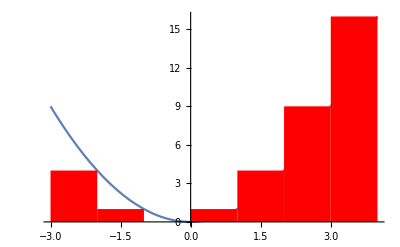

```mathematica
approximateIntegralPlot[x^2,{x,-3,4},"right",1]
```

```mathematica
averageValueOfFunction[f_,x_,a_,b_]:=1/(b-a)*Integrate[f,{x,a,b}]
```

```mathematica
nAverageValueOfFunction[f_,x_,a_,b_]:=1/(b-a)*NIntegrate[f,{x,a,b}]
```